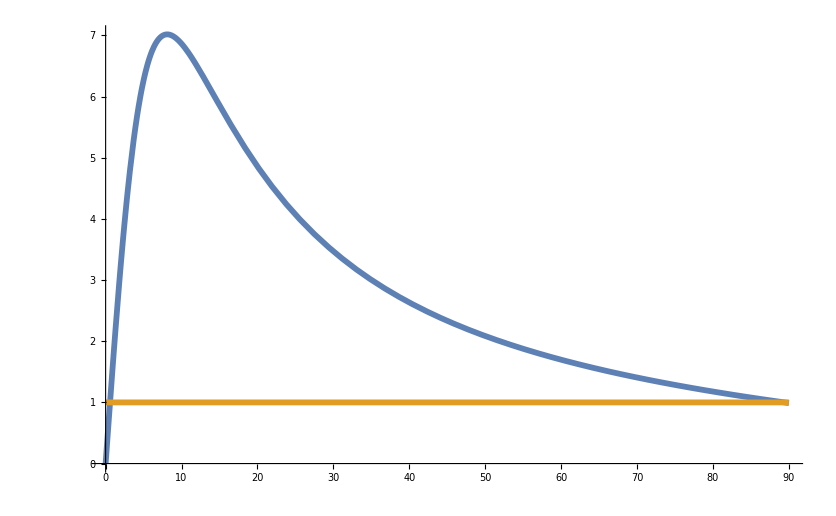

~/Dropbox/Documents/Sci_pop/Superluminal_jet/fig_7.png

```mathematica
Clear["Global`*"]
β=0.99;
<<MaTeX`
Plot[{(β Sin[x Pi/180])/(1-β Cos[x Pi/180]),1},{x,0,90},
TicksStyle->Large,Ticks->{Table[i,{i,0,100,10}],Table[i,{i,0,10}]},
AxesLabel->{MaTeX["\\theta, {}^\\circ",Magnification->3],MaTeX["\\beta",Magnification->3]},
PlotStyle->Thickness[0.005]]
Export["~/Dropbox/Documents/Sci_pop/Superluminal_jet/fig_7.png",%,ImageSize->1000,ImageResolution->1000]
```